Finding the parameters a,b of a beta distribution via likelihood maximization

First we simulate from a beta with known parameters

```mathematica
a=2; b=7;betasim=Table[RandomVariate[BetaDistribution[a,b]],{i,1,1000}];
```

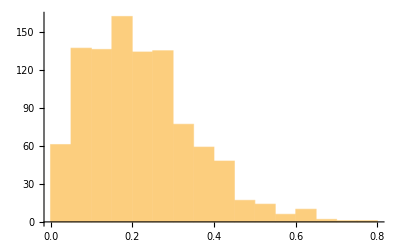

```mathematica
Histogram[betasim]
```

the likelihood can be written as:

```mathematica
ll[alpha_,beta_]:=Plus@@(Map[Log[PDF[BetaDistribution[alpha, beta],#]]&,betasim])
```

one might try to maximize directly with

```mathematica
Maximize[ll[alpha,beta],{alpha,beta}]
```

NMaximize::nrnum: The function value -1003.57-3141.59 ⅈ is not a real number at {alpha,beta} = {-0.535769,-0.13703}.

Maximize[Log[(0.499063^(-1+alpha) 0.500937^(-1+beta))/Beta[alpha,beta]]+Log[(1 1)/Beta[alpha,beta]]+996+Log[1]+Log[(0.0017676^(-1+alpha) 1)/Beta[alpha,beta]],1]
 |  |  |  |

but this would not work well because alpha and beta must be bigger than 0. Hence the correct optimization is

```mathematica
Maximize[ll[alpha,beta], alpha>0 && beta>0,{alpha,beta}]
```

{703.514,{alpha→1.98048,beta→6.9965}}

Alternatively, instead of writing explicit boundaries in the Maximize call
one can rewrite the likelihood in terms  of two auxiliary variables (which are not bound to be positive) alpha1=Log[alpha] and beta1=Log[beta]  as follows:

```mathematica
ll2[alpha1_,beta1_]:=Plus@@(Map[Log[PDF[BetaDistribution[Exp[alpha1], Exp[beta1]],#]]&,betasim])
```

```mathematica
Maximize[ll2[alpha1,beta1] ,{alpha1,beta1}]
```

{703.514,{alpha1→0.683342,beta1→1.94541}}

```mathematica
Exp[0.6833415077491054]
```

1.98048

```mathematica
Exp[1.9454095481839093]
```

6.9965